```mathematica
allGraphs5[lambdaKey,"colofour" ]/.RepGraph["C"]
```

-Graphics-361660+-Graphics-361120+-Graphics-317380+-Graphics-317140+-Graphics-296080+-Graphics-360850+-Graphics-317110+-Graphics-296050+-Graphics-295510+-Graphics-295270+-Graphics-295240

```mathematica
EdgeList[gr]
```

EdgeList[gr]

```mathematica
gr=Graph[EdgeAdd[VertexAdd[allGraphs5[lambdaKey,"graph" ],{6,7}],{1<->6,2<->6,5<->7}],VertexLabels->"Name"]
```

-Graphics-

```mathematica
EmbedGraphInGr[key_]:=Block[{val=allGraphs5[key], sets, g, sub},
sets=val["vertexsets"];
g=gr;
g=EdgeDelete[ g,{1<->2,1<->5,2<->3,3<->4,4<->5}];
Table[If[Length[s]>1,
g=VertexContract[g,s]
], {s,sets}];
sub=val["graph"];
Table[
g=EdgeAdd[g,{First[sets[[e[[1]]]]]<->First[sets[[e[[2]]]]]}],{e,EdgeList[sub]}];

Graph[VertexList[g],DeleteDuplicates[EdgeList[g]],VertexLabels->"Name"]
]
```

```mathematica
Select[Keys[allGraphs5],Length[ListofVars[allGraphs5[#,"colofour"]]]==2&]
```

{29523,29521,29529,29515,29517,29513,29542,29497,29506,29602,29577,29443,29446,29469,29417,29766,29737,29826,29677,29706,29648,29281,29282,29305,29257,29353,29378,29328,29209,29232,29186,30244,30172,30406,30010,30082,29938,28795,28804,28876,29038,29128,31708,31684,31924,31468,31492,31444,32198,30981,31224,27337,27340,27364,27580,27610,28065,28308,26609,26852,36084,36058,36138,36004,36030,35978,36736,35353,35434,38254,37548,33889,33916,34620,33158,22963,22964,22990,23044,23072,23689,23770,22237,22318,25141,25168,25868,24414,20785,20812,21510,20060,49206,49204,49212,49198,49200,49196,49954,48451,48460,51472,50718,46939,46942,47694,46184,56010,55252,57528,53734,54492,52976,42403,42404,43156,41650,44662,45416,43908,40144,40896,39392,9841,9842,9844,9850,9854,10543,10552,9139,9148,11947,11950,12650,11244,7735,7738,8436,7034,16159,16160,16864,15454,18274,18980,17568,14044,14748,13340,3523,3524,4222,2824,5620,6320,4920,1426,2124,728}

```mathematica
ListofVars[allGraphs5[29523,"colofour" ]]/.RepKey["C"]
```

{29525,29524}

```mathematica
ChromaticPolynomial[EmbedGraphInGr[29523],x]//Simplify
```

x (-6+11 x-6 x^2+x^3)^2

```mathematica
parts=Table[
With[{current=EmbedGraphInGr[atom]},
With[{left=VertexDelete[current,7],
right=VertexDelete[current,6]},
Simplify[(ChromaticPolynomial[left,x]*ChromaticPolynomial[right,x])/ChromaticPolynomial[allGraphs5[atom,"graph"],x]]
]
],
{atom,(ListofVars[allGraphs5[29523,"colofour" ]]/.RepKey["C"])}]
```

{(-2+x) (-1+x)^2 x (6-5 x+x^2),(-2+x) (-1+x)^2 x (-24+26 x-9 x^2+x^3)}

```mathematica
Total[parts]//Simplify
```

x (-6+11 x-6 x^2+x^3)^2

## Second example

```mathematica
Select[Keys[allGraphs5],35<Length[ListofVars[allGraphs5[#,"colofour"]]]&]
```

{0,19683,6561,2187,729,243,81,27,9,3,1}

```mathematica
ListofVars[allGraphs5[19683,"colofour" ]]/.RepKey["C"]
```

{39014,38308,38281,36898,36817,36194,36166,36112,36086,36085,32684,32441,31984,31954,31738,31714,31711,30586,30496,30334,30262,30253,29888,29857,29797,29768,29767,29633,29608,29605,29560,29551,29537,29533,29527,29525,29524}

```mathematica
ChromaticPolynomial[EmbedGraphInGr[19683],x]//Simplify
```

(-2+x) (-1+x)^2 x^4

```mathematica
parts=Table[
With[{current=EmbedGraphInGr[atom]},
With[{left=VertexDelete[current,7],
right=VertexDelete[current,6]},
Simplify[(ChromaticPolynomial[left,x]*ChromaticPolynomial[right,x])/ChromaticPolynomial[allGraphs5[atom,"graph"],x]]
]
],
{atom,(ListofVars[allGraphs5[19683,"colofour" ]]/.RepKey["C"])}]
```

{(-2+x) (-1+x)^2 x,(-2+x) (-1+x)^2 x,(-2+x)^2 (-1+x)^2 x,(-2+x) (-1+x)^2 x,(-2+x)^2 (-1+x)^2 x,(-2+x) (-1+x)^2 x,(-2+x)^2 (-1+x)^2 x,(-2+x)^2 (-1+x)^2 x,(-2+x)^2 (-1+x)^2 x,(-2+x) (-1+x)^2 x (6-5 x+x^2),(-2+x) (-1+x)^2 x,(-2+x)^2 (-1+x)^2 x,(-2+x) (-1+x)^2 x,(-2+x)^2 (-1+x)^2 x,(-2+x)^2 (-1+x)^2 x,(-2+x)^2 (-1+x)^2 x,(-2+x) (-1+x)^2 x (6-5 x+x^2),(-2+x) (-1+x)^2 x,(-2+x)^2 (-1+x)^2 x,(-2+x)^2 (-1+x)^2 x,(-2+x)^2 (-1+x)^2 x,(-2+x) (-1+x)^2 x (6-5 x+x^2),(-2+x) (-1+x)^2 x,(-2+x)^2 (-1+x)^2 x,(-2+x)^2 (-1+x)^2 x,(-2+x)^2 (-1+x)^2 x,(-2+x) (-1+x)^2 x (6-5 x+x^2),(-2+x)^2 (-1+x)^2 x,(-2+x)^2 (-1+x)^2 x,(-2+x) (-1+x)^2 x (6-5 x+x^2),(-2+x)^2 (-1+x)^2 x,(-2+x) (-1+x)^2 x (6-5 x+x^2),(-2+x)^2 (-1+x)^2 x,(-2+x) (-1+x)^2 x (6-5 x+x^2),(-2+x) (-1+x)^2 x (6-5 x+x^2),(-2+x) (-1+x)^2 x (6-5 x+x^2),(-2+x) (-1+x)^2 x (-24+26 x-9 x^2+x^3)}

```mathematica
Total[parts]//Simplify
```

(-2+x) (-1+x)^2 x^4

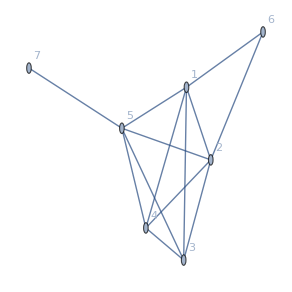

```mathematica
EmbedGraphInGr[K5Key]
```

## Thrid example

```mathematica
gr=Graph[EdgeAdd[VertexAdd[allGraphs5[lambdaKey,"graph" ],{6,7,8}],{1<->6,2<->6,5<->7,5<->7,4<->7,4<->8,4<->8}],VertexLabels->"Name"]
```

-Graphics-

```mathematica
ListofVars[allGraphs5[19683,"colofour" ]]/.RepKey["C"]
```

{39014,38308,38281,36898,36817,36194,36166,36112,36086,36085,32684,32441,31984,31954,31738,31714,31711,30586,30496,30334,30262,30253,29888,29857,29797,29768,29767,29633,29608,29605,29560,29551,29537,29533,29527,29525,29524}

```mathematica
ChromaticPolynomial[EmbedGraphInGr[19683],x]//Simplify
```

(-2+x) (-1+x)^4 x^3

```mathematica
parts=Table[
With[{current=EmbedGraphInGr[atom]},
With[{left=VertexDelete[current,{7,8}],
right=VertexDelete[current,6]},
Simplify[(ChromaticPolynomial[left,x]*ChromaticPolynomial[right,x])/ChromaticPolynomial[allGraphs5[atom,"graph"],x]]
]
],
{atom,(ListofVars[allGraphs5[19683,"colofour" ]]/.RepKey["C"])}]
```

{(-2+x) (-1+x)^3 x,(-2+x)^2 (-1+x)^2 x,(-2+x) x (2-3 x+x^2)^2,(-2+x)^2 (-1+x)^2 x,(-2+x) x (2-3 x+x^2)^2,(-2+x) (-1+x)^3 x,(-2+x) x (2-3 x+x^2)^2,(-2+x) x (2-3 x+x^2)^2,(-2+x)^2 (-1+x)^3 x,(-3+x) (-2+x) x (2-3 x+x^2)^2,(-2+x) (-1+x)^3 x,(-2+x)^2 (-1+x)^3 x,(-2+x)^2 (-1+x)^2 x,(-2+x) x (2-3 x+x^2)^2,(-2+x) x (2-3 x+x^2)^2,(-2+x) x (2-3 x+x^2)^2,(-3+x) (-2+x) x (2-3 x+x^2)^2,(-2+x)^2 (-1+x)^2 x,(-2+x) x (2-3 x+x^2)^2,(-2+x) x (2-3 x+x^2)^2,(-2+x) x (2-3 x+x^2)^2,(-3+x) (-2+x) x (2-3 x+x^2)^2,(-2+x) (-1+x)^3 x,(-2+x) x (2-3 x+x^2)^2,(-2+x) x (2-3 x+x^2)^2,(-2+x)^2 (-1+x)^3 x,(-3+x) (-2+x) x (2-3 x+x^2)^2,(-2+x)^2 (-1+x)^3 x,(-2+x) x (2-3 x+x^2)^2,(-3+x) (-2+x) x (2-3 x+x^2)^2,(-2+x) x (2-3 x+x^2)^2,(-3+x) (-2+x) x (2-3 x+x^2)^2,(-2+x)^2 (-1+x)^3 x,(-3+x) (-2+x) x (2-3 x+x^2)^2,(-3+x) (-2+x) x (2-3 x+x^2)^2,(-2+x) (-1+x)^3 x (6-5 x+x^2),(-2+x) x (12-7 x+x^2) (2-3 x+x^2)^2}

```mathematica
ListofVars[allGraphs5[19683,"colofourgenerator" ]]/.RepKey["G"]
```

{20034,20740,22150,22854,26364,27064,28462,29160,20767,22231,22882,22936,22962,22963,26607,27094,27310,27334,27337,28552,28714,28786,28795,29191,29251,29280,29281,29415,29440,29443,29488,29497,29511,29515,29521,29523,29524}

```mathematica
Total[parts]//Simplify
```

(-2+x) (-1+x)^4 x^3

```mathematica
parts=With[
{formula=allGraphs5[19683,"colofourgenerator" ]},
Table[
With[{current=EmbedGraphInGr[atom]},
With[{left=VertexDelete[current,{7,8}],
right=VertexDelete[current,6]},
Coefficient[formula,allGraphs5[atom,"colofourgenerator"]]*Simplify[(ChromaticPolynomial[left,x]*ChromaticPolynomial[right,x])/ChromaticPolynomial[allGraphs5[atom,"graph"],x]]
]
],
{atom,(ListofVars[formula]/.RepKey["G"])}]
]
```

{(-2+x) (-1+x)^4 x (3-3 x+x^2),(-2+x) (-1+x)^2 x (14-27 x+20 x^2-7 x^3+x^4),(-2+x) (-1+x)^2 x (14-27 x+20 x^2-7 x^3+x^4),(-2+x) (-1+x)^2 x (17-30 x+21 x^2-7 x^3+x^4),(-2+x) (-1+x)^2 x (17-30 x+21 x^2-7 x^3+x^4),(-2+x) (-1+x)^2 x (14-27 x+20 x^2-7 x^3+x^4),(-2+x) (-1+x)^2 x (14-27 x+20 x^2-7 x^3+x^4),(-2+x) (-1+x)^4 x (3-3 x+x^2),-(-2+x)^5 (-1+x)^2 x,-(-2+x)^5 (-1+x)^2 x,-(-2+x) x (7-5 x+x^2) (2-3 x+x^2)^2,-(-2+x) x (7-5 x+x^2) (2-3 x+x^2)^2,-(-2+x) x (8-5 x+x^2) (2-3 x+x^2)^2,2 (-2+x) x (-6+11 x-6 x^2+x^3)^2,-(-2+x) x (5-4 x+x^2) (2-3 x+x^2)^2,-(-2+x) x (7-5 x+x^2) (2-3 x+x^2)^2,-(-2+x) x (7-5 x+x^2) (2-3 x+x^2)^2,-(-2+x) x (7-5 x+x^2) (2-3 x+x^2)^2,2 (-2+x) x (-6+11 x-6 x^2+x^3)^2,-(-2+x) x (7-5 x+x^2) (2-3 x+x^2)^2,-(-2+x) x (7-5 x+x^2) (2-3 x+x^2)^2,-(-2+x) x (7-5 x+x^2) (2-3 x+x^2)^2,2 (-2+x) x (-6+11 x-6 x^2+x^3)^2,-(-2+x)^5 (-1+x)^2 x,-(-2+x)^5 (-1+x)^2 x,-(-2+x) x (8-5 x+x^2) (2-3 x+x^2)^2,2 (-2+x) x (-6+11 x-6 x^2+x^3)^2,-(-2+x) x (5-4 x+x^2) (2-3 x+x^2)^2,-(-2+x) x (7-5 x+x^2) (2-3 x+x^2)^2,2 (-2+x) x (-6+11 x-6 x^2+x^3)^2,-(-2+x) x (7-5 x+x^2) (2-3 x+x^2)^2,2 (-2+x) x (-6+11 x-6 x^2+x^3)^2,-(-2+x) x (5-4 x+x^2) (2-3 x+x^2)^2,2 (-2+x) x (-6+11 x-6 x^2+x^3)^2,2 (-2+x) x (-6+11 x-6 x^2+x^3)^2,2 (-2+x) (-1+x)^2 x (42-65 x+38 x^2-10 x^3+x^4),-6 (-2+x) x (12-7 x+x^2) (2-3 x+x^2)^2}

```mathematica
Total[parts]//FullSimplify
```

(-2+x) (-1+x)^4 x^3

```mathematica
parts=With[{base="G"},
With[
{formula=allGraphs5[19683,Bases[base,"Colofour"] ]},
Table[
With[{current=EmbedGraphInGr[atom]},
With[{left=VertexDelete[current,{7,8}],
right=VertexDelete[current,6]},
Coefficient[formula,allGraphs5[atom,Bases[base,"Colofour"]]]*Simplify[(ChromaticPolynomial[left,x]*ChromaticPolynomial[right,x])/ChromaticPolynomial[allGraphs5[atom,"graph"],x]]
]
],
{atom,(ListofVars[formula]/.RepKey[base])}]
]
]
```

{(-2+x) (-1+x)^4 x (3-3 x+x^2),(-2+x) (-1+x)^2 x (14-27 x+20 x^2-7 x^3+x^4),(-2+x) (-1+x)^2 x (14-27 x+20 x^2-7 x^3+x^4),(-2+x) (-1+x)^2 x (17-30 x+21 x^2-7 x^3+x^4),(-2+x) (-1+x)^2 x (17-30 x+21 x^2-7 x^3+x^4),(-2+x) (-1+x)^2 x (14-27 x+20 x^2-7 x^3+x^4),(-2+x) (-1+x)^2 x (14-27 x+20 x^2-7 x^3+x^4),(-2+x) (-1+x)^4 x (3-3 x+x^2),-(-2+x)^5 (-1+x)^2 x,-(-2+x)^5 (-1+x)^2 x,-(-2+x) x (7-5 x+x^2) (2-3 x+x^2)^2,-(-2+x) x (7-5 x+x^2) (2-3 x+x^2)^2,-(-2+x) x (8-5 x+x^2) (2-3 x+x^2)^2,2 (-2+x) x (-6+11 x-6 x^2+x^3)^2,-(-2+x) x (5-4 x+x^2) (2-3 x+x^2)^2,-(-2+x) x (7-5 x+x^2) (2-3 x+x^2)^2,-(-2+x) x (7-5 x+x^2) (2-3 x+x^2)^2,-(-2+x) x (7-5 x+x^2) (2-3 x+x^2)^2,2 (-2+x) x (-6+11 x-6 x^2+x^3)^2,-(-2+x) x (7-5 x+x^2) (2-3 x+x^2)^2,-(-2+x) x (7-5 x+x^2) (2-3 x+x^2)^2,-(-2+x) x (7-5 x+x^2) (2-3 x+x^2)^2,2 (-2+x) x (-6+11 x-6 x^2+x^3)^2,-(-2+x)^5 (-1+x)^2 x,-(-2+x)^5 (-1+x)^2 x,-(-2+x) x (8-5 x+x^2) (2-3 x+x^2)^2,2 (-2+x) x (-6+11 x-6 x^2+x^3)^2,-(-2+x) x (5-4 x+x^2) (2-3 x+x^2)^2,-(-2+x) x (7-5 x+x^2) (2-3 x+x^2)^2,2 (-2+x) x (-6+11 x-6 x^2+x^3)^2,-(-2+x) x (7-5 x+x^2) (2-3 x+x^2)^2,2 (-2+x) x (-6+11 x-6 x^2+x^3)^2,-(-2+x) x (5-4 x+x^2) (2-3 x+x^2)^2,2 (-2+x) x (-6+11 x-6 x^2+x^3)^2,2 (-2+x) x (-6+11 x-6 x^2+x^3)^2,2 (-2+x) (-1+x)^2 x (42-65 x+38 x^2-10 x^3+x^4),-6 (-2+x) x (12-7 x+x^2) (2-3 x+x^2)^2}

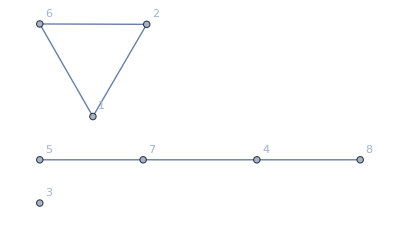

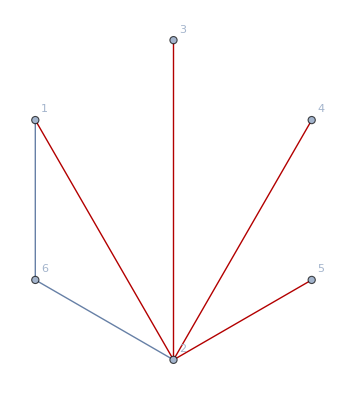
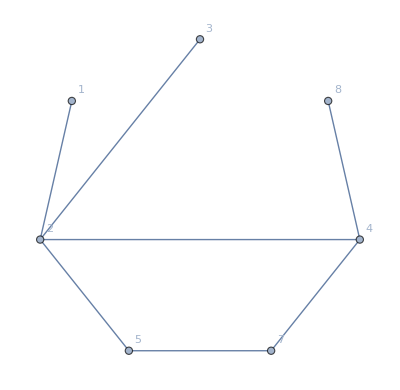
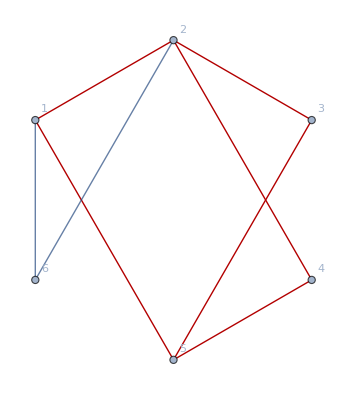
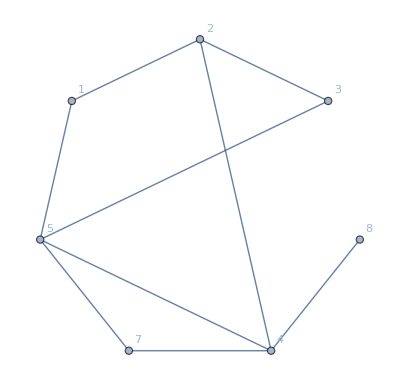
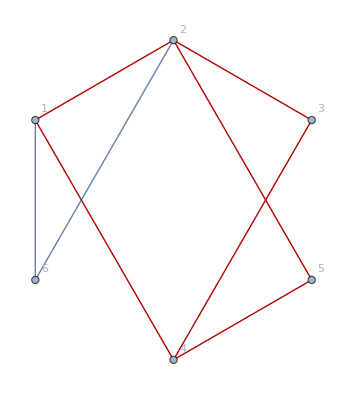
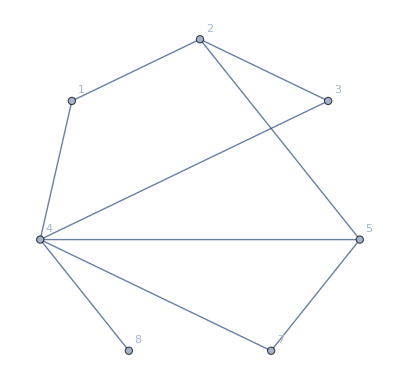
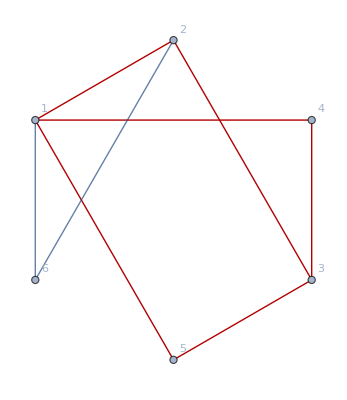
{(-Graphics- -Graphics-{1<->2,2<->3,2<->4,2<->5})/(-Graphics-),(-Graphics- -Graphics-{1<->2,1<->5,2<->3,2<->4,3<->5,4<->5})/(-Graphics-),(-Graphics- -Graphics-{1<->2,1<->4,2<->3,2<->5,3<->4,4<->5})/(-Graphics-),(-Graphics- -Graphics-{1<->2,1<->4,1<->5,2<->3,3<->4,3<->5})/(-Graphics-),(-Graphics- -Graphics-{1<->2,1<->3,2<->4,2<->5,3<->4,3<->5})/(-Graphics-),(-Graphics- -Graphics-{1<->2,1<->3,1<->5,2<->4,3<->4,4<->5})/(-Graphics-),(-Graphics- -Graphics-{1<->2,1<->3,1<->4,2<->5,3<->5,4<->5})/(-Graphics-),(-Graphics- -Graphics-{1<->2,1<->3,1<->4,1<->5})/(-Graphics-),-(-Graphics- -Graphics-{1<->2,1<->5,2<->3,2<->4,2<->5,3<->5,4<->5})/(-Graphics-),-(-Graphics- -Graphics-{1<->2,1<->4,2<->3,2<->4,2<->5,3<->4,4<->5})/(-Graphics-),-(-Graphics- -Graphics-{1<->2,1<->4,1<->5,2<->3,2<->5,3<->4,3<->5,4<->5})/(-Graphics-),-(-Graphics- -Graphics-{1<->2,1<->4,1<->5,2<->3,2<->4,3<->4,3<->5,4<->5})/(-Graphics-),-(-Graphics- -Graphics-{1<->2,1<->4,1<->5,2<->3,2<->4,2<->5,3<->4,3<->5})/(-Graphics-),(2 -Graphics- -Graphics-{1<->2,1<->4,1<->5,2<->3,2<->4,2<->5,3<->4,3<->5,4<->5})/(-Graphics-),-(-Graphics- -Graphics-{1<->2,1<->3,2<->3,2<->4,2<->5,3<->4,3<->5})/(-Graphics-),-(-Graphics- -Graphics-{1<->2,1<->3,1<->5,2<->4,2<->5,3<->4,3<->5,4<->5})/(-Graphics-),-(-Graphics- -Graphics-{1<->2,1<->3,1<->5,2<->3,2<->4,3<->4,3<->5,4<->5})/(-Graphics-),-(-Graphics- -Graphics-{1<->2,1<->3,1<->5,2<->3,2<->4,2<->5,3<->4,4<->5})/(-Graphics-),(2 -Graphics- -Graphics-{1<->2,1<->3,1<->5,2<->3,2<->4,2<->5,3<->4,3<->5,4<->5})/(-Graphics-),-(-Graphics- -Graphics-{1<->2,1<->3,1<->4,2<->4,2<->5,3<->4,3<->5,4<->5})/(-Graphics-),-(-Graphics- -Graphics-{1<->2,1<->3,1<->4,2<->3,2<->5,3<->4,3<->5,4<->5})/(-Graphics-),-(-Graphics- -Graphics-{1<->2,1<->3,1<->4,2<->3,2<->4,2<->5,3<->5,4<->5})/(-Graphics-),(2 -Graphics- -Graphics-{1<->2,1<->3,1<->4,2<->3,2<->4,2<->5,3<->4,3<->5,4<->5})/(-Graphics-),-(-Graphics- -Graphics-{1<->2,1<->3,1<->4,1<->5,2<->5,3<->5,4<->5})/(-Graphics-),-(-Graphics- -Graphics-{1<->2,1<->3,1<->4,1<->5,2<->4,3<->4,4<->5})/(-Graphics-),-(-Graphics- -Graphics-{1<->2,1<->3,1<->4,1<->5,2<->4,2<->5,3<->4,3<->5})/(-Graphics-),(2 -Graphics- -Graphics-{1<->2,1<->3,1<->4,1<->5,2<->4,2<->5,3<->4,3<->5,4<->5})/(-Graphics-),-(-Graphics- -Graphics-{1<->2,1<->3,1<->4,1<->5,2<->3,3<->4,3<->5})/(-Graphics-),-(-Graphics- -Graphics-{1<->2,1<->3,1<->4,1<->5,2<->3,2<->5,3<->4,4<->5})/(-Graphics-),(2 -Graphics- -Graphics-{1<->2,1<->3,1<->4,1<->5,2<->3,2<->5,3<->4,3<->5,4<->5})/(-Graphics-),-(-Graphics- -Graphics-{1<->2,1<->3,1<->4,1<->5,2<->3,2<->4,3<->5,4<->5})/(-Graphics-),(2 -Graphics- -Graphics-{1<->2,1<->3,1<->4,1<->5,2<->3,2<->4,3<->4,3<->5,4<->5})/(-Graphics-),-(-Graphics- -Graphics-{1<->2,1<->3,1<->4,1<->5,2<->3,2<->4,2<->5})/(-Graphics-),(2 -Graphics- -Graphics-{1<->2,1<->3,1<->4,1<->5,2<->3,2<->4,2<->5,3<->5,4<->5})/(-Graphics-),(2 -Graphics- -Graphics-{1<->2,1<->3,1<->4,1<->5,2<->3,2<->4,2<->5,3<->4,4<->5})/(-Graphics-),(2 -Graphics- -Graphics-{1<->2,1<->3,1<->4,1<->5,2<->3,2<->4,2<->5,3<->4,3<->5})/(-Graphics-),-(6 -Graphics- -Graphics-{1<->2,1<->3,1<->4,1<->5,2<->3,2<->4,2<->5,3<->4,3<->5,4<->5})/(-Graphics-)}

```mathematica
With[{base="G"},
With[
{formula=allGraphs5[19683,Bases[base,"Colofour"] ]},
Print[EmbedGraphInGr[19683]];
Table[
With[{current=EmbedGraphInGr[atom]},
With[{left=VertexDelete[current,{7,8}],
right=VertexDelete[current,6]},
Coefficient[formula,allGraphs5[atom,Bases[base,"Colofour"]]]*Simplify[(Graph[left,GraphLayout->"CircularEmbedding",GraphHighlight->EdgeList[allGraphs5[atom,"graph"]]]*Labeled[Graph[right,GraphLayout->"CircularEmbedding",GraphHighlight->EdgeList[allGraphs5[atom,"graph"]]],EdgeList[allGraphs5[atom,"graph"]]])/allGraphs5[atom,"graph"]]
]
],
{atom,(ListofVars[formula]/.RepKey[base])}]
]
]
```

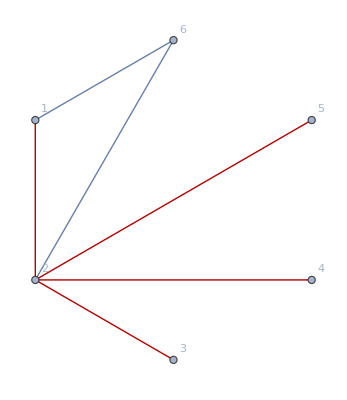
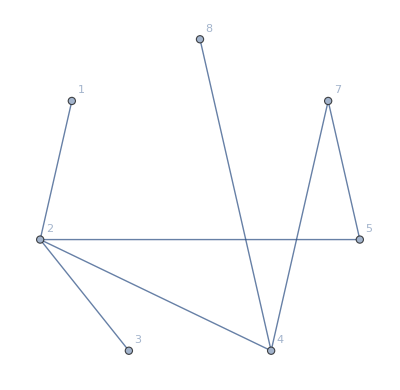
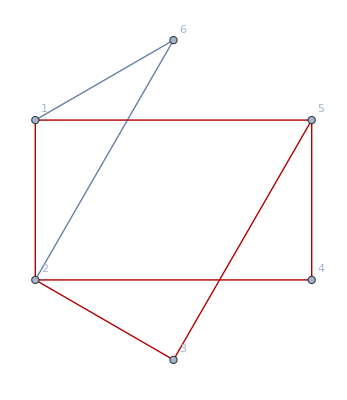
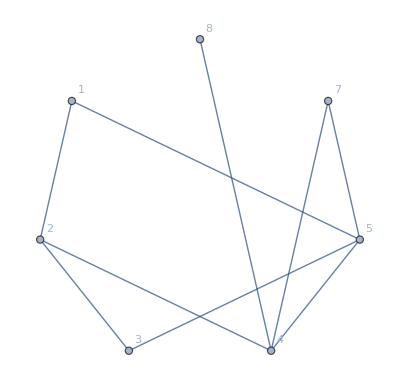
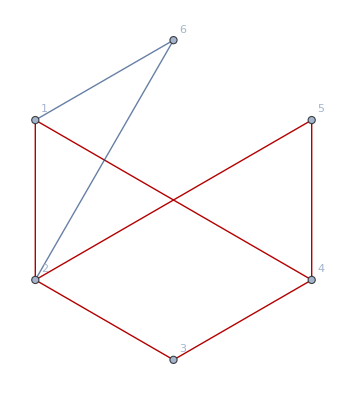
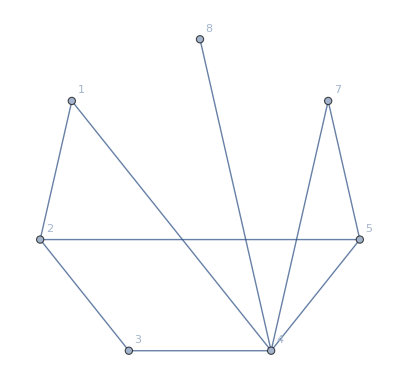
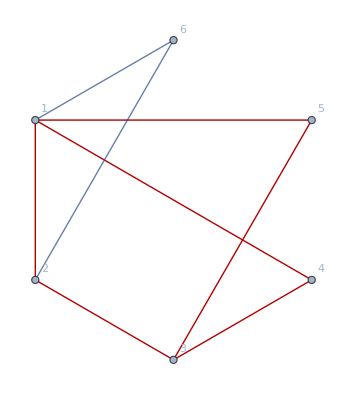
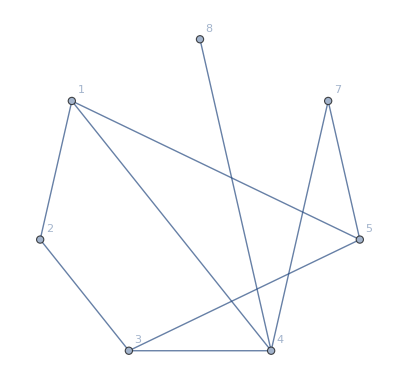
```mathematica
{(-Graphics- -Graphics-{1<->2,2<->3,2<->4,2<->5})/(-Graphics-),(-Graphics- -Graphics-{1<->2,1<->5,2<->3,2<->4,3<->5,4<->5})/(-Graphics-),(-Graphics- -Graphics-{1<->2,1<->4,2<->3,2<->5,3<->4,4<->5})/(-Graphics-),(-Graphics- -Graphics-{1<->2,1<->4,1<->5,2<->3,3<->4,3<->5})/(-Graphics-),(-Graphics- -Graphics-{1<->2,1<->3,2<->4,2<->5,3<->4,3<->5})/(-Graphics-),(-Graphics- -Graphics-{1<->2,1<->3,1<->5,2<->4,3<->4,4<->5})/(-Graphics-),(-Graphics- -Graphics-{1<->2,1<->3,1<->4,2<->5,3<->5,4<->5})/(-Graphics-),(-Graphics- -Graphics-{1<->2,1<->3,1<->4,1<->5})/(-Graphics-),-(-Graphics- -Graphics-{1<->2,1<->5,2<->3,2<->4,2<->5,3<->5,4<->5})/(-Graphics-),-(-Graphics- -Graphics-{1<->2,1<->4,2<->3,2<->4,2<->5,3<->4,4<->5})/(-Graphics-),-(-Graphics- -Graphics-{1<->2,1<->4,1<->5,2<->3,2<->5,3<->4,3<->5,4<->5})/(-Graphics-),-(-Graphics- -Graphics-{1<->2,1<->4,1<->5,2<->3,2<->4,3<->4,3<->5,4<->5})/(-Graphics-),-(-Graphics- -Graphics-{1<->2,1<->4,1<->5,2<->3,2<->4,2<->5,3<->4,3<->5})/(-Graphics-),(2 -Graphics- -Graphics-{1<->2,1<->4,1<->5,2<->3,2<->4,2<->5,3<->4,3<->5,4<->5})/(-Graphics-),-(-Graphics- -Graphics-{1<->2,1<->3,2<->3,2<->4,2<->5,3<->4,3<->5})/(-Graphics-),-(-Graphics- -Graphics-{1<->2,1<->3,1<->5,2<->4,2<->5,3<->4,3<->5,4<->5})/(-Graphics-),-(-Graphics- -Graphics-{1<->2,1<->3,1<->5,2<->3,2<->4,3<->4,3<->5,4<->5})/(-Graphics-),-(-Graphics- -Graphics-{1<->2,1<->3,1<->5,2<->3,2<->4,2<->5,3<->4,4<->5})/(-Graphics-),(2 -Graphics- -Graphics-{1<->2,1<->3,1<->5,2<->3,2<->4,2<->5,3<->4,3<->5,4<->5})/(-Graphics-),-(-Graphics- -Graphics-{1<->2,1<->3,1<->4,2<->4,2<->5,3<->4,3<->5,4<->5})/(-Graphics-),-(-Graphics- -Graphics-{1<->2,1<->3,1<->4,2<->3,2<->5,3<->4,3<->5,4<->5})/(-Graphics-),-(-Graphics- -Graphics-{1<->2,1<->3,1<->4,2<->3,2<->4,2<->5,3<->5,4<->5})/(-Graphics-),(2 -Graphics- -Graphics-{1<->2,1<->3,1<->4,2<->3,2<->4,2<->5,3<->4,3<->5,4<->5})/(-Graphics-),-(-Graphics- -Graphics-{1<->2,1<->3,1<->4,1<->5,2<->5,3<->5,4<->5})/(-Graphics-),-(-Graphics- -Graphics-{1<->2,1<->3,1<->4,1<->5,2<->4,3<->4,4<->5})/(-Graphics-),-(-Graphics- -Graphics-{1<->2,1<->3,1<->4,1<->5,2<->4,2<->5,3<->4,3<->5})/(-Graphics-),(2 -Graphics- -Graphics-{1<->2,1<->3,1<->4,1<->5,2<->4,2<->5,3<->4,3<->5,4<->5})/(-Graphics-),-(-Graphics- -Graphics-{1<->2,1<->3,1<->4,1<->5,2<->3,3<->4,3<->5})/(-Graphics-),-(-Graphics- -Graphics-{1<->2,1<->3,1<->4,1<->5,2<->3,2<->5,3<->4,4<->5})/(-Graphics-),(2 -Graphics- -Graphics-{1<->2,1<->3,1<->4,1<->5,2<->3,2<->5,3<->4,3<->5,4<->5})/(-Graphics-),-(-Graphics- -Graphics-{1<->2,1<->3,1<->4,1<->5,2<->3,2<->4,3<->5,4<->5})/(-Graphics-),(2 -Graphics- -Graphics-{1<->2,1<->3,1<->4,1<->5,2<->3,2<->4,3<->4,3<->5,4<->5})/(-Graphics-),-(-Graphics- -Graphics-{1<->2,1<->3,1<->4,1<->5,2<->3,2<->4,2<->5})/(-Graphics-),(2 -Graphics- -Graphics-{1<->2,1<->3,1<->4,1<->5,2<->3,2<->4,2<->5,3<->5,4<->5})/(-Graphics-),(2 -Graphics- -Graphics-{1<->2,1<->3,1<->4,1<->5,2<->3,2<->4,2<->5,3<->4,4<->5})/(-Graphics-), (2 -Graphics- -Graphics-{1<->2,1<->3,1<->4,1<->5,2<->3,2<->4,2<->5,3<->4,3<->5})/(-Graphics-),-(6 -Graphics- -Graphics-{1<->2,1<->3,1<->4,1<->5,2<->3,2<->4,2<->5,3<->4,3<->5,4<->5})/(-Graphics-)}
```

{1/(-Graphics-)Graph[{1,2,3,4,5,6},{Null,{{1,6},{2,6},{1,2},{2,3},{2,4},{2,5}}},{FormatType→TraditionalForm,GraphHighlight→{1<->2,2<->5,2<->3,2<->4},GraphLayout→{Dimension→2,VertexLayout→CircularEmbedding},VertexLabels→{Name,8→None,7→None}}] Graph[{1,2,3,4,5,7,8},{Null,{{5,6},{4,6},{4,7},{1,2},{2,3},{2,4},{2,5}}},{FormatType→TraditionalForm,GraphHighlight→{1<->2,2<->3,2<->5,2<->4},GraphLayout→{Dimension→2,VertexLayout→CircularEmbedding},VertexLabels→{Name,6→None}}]{1<->2,2<->3,2<->4,2<->5},1/(-Graphics-)Graph[{1,2,3,4,5,6},{Null,{{1,6},{2,6},{1,2},{1,5},{2,3},{2,4},{3,5},{4,5}}},{FormatType→TraditionalForm,GraphHighlight→{4<->5,1<->2,3<->5,2<->3,1<->5,2<->4},GraphLayout→{Dimension→2,VertexLayout→CircularEmbedding},VertexLabels→{Name,8→None,7→None}}] Graph[{1,2,3,4,5,7,8},{Null,{{5,6},{4,6},{4,7},{1,2},{1,5},{2,3},{2,4},{3,5},{4,5}}},{FormatType→TraditionalForm,GraphHighlight→{3<->5,1<->2,2<->3,4<->5,2<->4,1<->5},GraphLayout→{Dimension→2,VertexLayout→CircularEmbedding},VertexLabels→{Name,6→None}}]{1<->2,1<->5,2<->3,2<->4,3<->5,4<->5},1/(-Graphics-)Graph[{1,2,3,4,5,6},{Null,{{1,6},{2,6},{1,2},{1,4},{2,3},{2,5},{3,4},{4,5}}},{FormatType→TraditionalForm,GraphHighlight→{3<->4,4<->5,1<->2,2<->5,2<->3,1<->4},GraphLayout→{Dimension→2,VertexLayout→CircularEmbedding},VertexLabels→{Name,8→None,7→None}}] Graph[{1,2,3,4,5,7,8},{Null,{{5,6},{4,6},{4,7},{1,2},{1,4},{2,3},{2,5},{3,4},{4,5}}},{FormatType→TraditionalForm,GraphHighlight→{1<->2,2<->3,1<->4,4<->5,3<->4,2<->5},GraphLayout→{Dimension→2,VertexLayout→CircularEmbedding},VertexLabels→{Name,6→None}}]{1<->2,1<->4,2<->3,2<->5,3<->4,4<->5},1/(-Graphics-)Graph[{1,2,3,4,5,6},{Null,{{1,6},{2,6},{1,2},{1,4},{1,5},{2,3},{3,4},{3,5}}},{FormatType→TraditionalForm,GraphHighlight→{3<->4,1<->2,3<->5,2<->3,1<->5,1<->4},GraphLayout→{Dimension→2,VertexLayout→CircularEmbedding},VertexLabels→{Name,8→None,7→None}}] Graph[{1,2,3,4,5,7,8},{Null,{{5,6},{4,6},{4,7},{1,2},{1,4},{1,5},{2,3},{3,4},{3,5}}},{FormatType→TraditionalForm,GraphHighlight→{3<->5,1<->2,2<->3,1<->4,3<->4,1<->5},GraphLayout→{Dimension→2,VertexLayout→CircularEmbedding},VertexLabels→{Name,6→None}}]{1<->2,1<->4,1<->5,2<->3,3<->4,3<->5},1/(-Graphics-)Graph[{1,2,3,4,5,6},{Null,{{1,6},{2,6},{1,2},{1,3},{2,4},{2,5},{3,4},{3,5}}},{FormatType→TraditionalForm,GraphHighlight→{3<->4,1<->2,3<->5,2<->5,1<->3,2<->4},GraphLayout→{Dimension→2,VertexLayout→CircularEmbedding},VertexLabels→{Name,8→None,7→None}}] Graph[{1,2,3,4,5,7,8},{Null,{{5,6},{4,6},{4,7},{1,2},{1,3},{2,4},{2,5},{3,4},{3,5}}},{FormatType→TraditionalForm,GraphHighlight→{3<->5,1<->2,1<->3,3<->4,2<->5,2<->4},GraphLayout→{Dimension→2,VertexLayout→CircularEmbedding},VertexLabels→{Name,6→None}}]{1<->2,1<->3,2<->4,2<->5,3<->4,3<->5},1/(-Graphics-)Graph[{1,2,3,4,5,6},{Null,{{1,6},{2,6},{1,2},{1,3},{1,5},{2,4},{3,4},{4,5}}},{FormatType→TraditionalForm,GraphHighlight→{3<->4,4<->5,1<->2,1<->5,1<->3,2<->4},GraphLayout→{Dimension→2,VertexLayout→CircularEmbedding},VertexLabels→{Name,8→None,7→None}}] Graph[{1,2,3,4,5,7,8},{Null,{{5,6},{4,6},{4,7},{1,2},{1,3},{1,5},{2,4},{3,4},{4,5}}},{FormatType→TraditionalForm,GraphHighlight→{1<->2,1<->3,4<->5,3<->4,2<->4,1<->5},GraphLayout→{Dimension→2,VertexLayout→CircularEmbedding},VertexLabels→{Name,6→None}}]{1<->2,1<->3,1<->5,2<->4,3<->4,4<->5},1/(-Graphics-)Graph[{1,2,3,4,5,6},{Null,{{1,6},{2,6},{1,2},{1,3},{1,4},{2,5},{3,5},{4,5}}},{FormatType→TraditionalForm,GraphHighlight→{4<->5,1<->2,3<->5,2<->5,1<->4,1<->3},GraphLayout→{Dimension→2,VertexLayout→CircularEmbedding},VertexLabels→{Name,8→None,7→None}}] Graph[{1,2,3,4,5,7,8},{Null,{{5,6},{4,6},{4,7},{1,2},{1,3},{1,4},{2,5},{3,5},{4,5}}},{FormatType→TraditionalForm,GraphHighlight→{3<->5,1<->2,1<->3,1<->4,4<->5,2<->5},GraphLayout→{Dimension→2,VertexLayout→CircularEmbedding},VertexLabels→{Name,6→None}}]{1<->2,1<->3,1<->4,2<->5,3<->5,4<->5},1/(-Graphics-)Graph[{1,2,3,4,5,6},{Null,{{1,6},{2,6},{1,2},{1,3},{1,4},{1,5}}},{FormatType→TraditionalForm,GraphHighlight→{1<->2,1<->5,1<->4,1<->3},GraphLayout→{Dimension→2,VertexLayout→CircularEmbedding},VertexLabels→{Name,8→None,7→None}}] Graph[{1,2,3,4,5,7,8},{Null,{{5,6},{4,6},{4,7},{1,2},{1,3},{1,4},{1,5}}},{FormatType→TraditionalForm,GraphHighlight→{1<->2,1<->3,1<->4,1<->5},GraphLayout→{Dimension→2,VertexLayout→CircularEmbedding},VertexLabels→{Name,6→None}}]{1<->2,1<->3,1<->4,1<->5},-1/(-Graphics-)Graph[{1,2,3,4,5,6},{Null,{{1,6},{2,6},{1,2},{1,5},{2,3},{2,4},{2,5},{3,5},{4,5}}},{FormatType→TraditionalForm,GraphHighlight→{4<->5,1<->2,3<->5,2<->5,2<->3,1<->5,2<->4},GraphLayout→{Dimension→2,VertexLayout→CircularEmbedding},VertexLabels→{Name,8→None,7→None}}] Graph[{1,2,3,4,5,7,8},{Null,{{5,6},{4,6},{4,7},{1,2},{1,5},{2,3},{2,4},{2,5},{3,5},{4,5}}},{FormatType→TraditionalForm,GraphHighlight→{4<->5,1<->2,3<->5,1<->5,2<->5,2<->3,2<->4},GraphLayout→{Dimension→2,VertexLayout→CircularEmbedding},VertexLabels→{Name,6→None}}]{1<->2,1<->5,2<->3,2<->4,2<->5,3<->5,4<->5},-1/(-Graphics-)Graph[{1,2,3,4,5,6},{Null,{{1,6},{2,6},{1,2},{1,4},{2,3},{2,4},{2,5},{3,4},{4,5}}},{FormatType→TraditionalForm,GraphHighlight→{3<->4,4<->5,1<->2,2<->5,2<->3,1<->4,2<->4},GraphLayout→{Dimension→2,VertexLayout→CircularEmbedding},VertexLabels→{Name,8→None,7→None}}] Graph[{1,2,3,4,5,7,8},{Null,{{5,6},{4,6},{4,7},{1,2},{1,4},{2,3},{2,4},{2,5},{3,4},{4,5}}},{FormatType→TraditionalForm,GraphHighlight→{3<->4,4<->5,1<->2,2<->5,1<->4,2<->3,2<->4},GraphLayout→{Dimension→2,VertexLayout→CircularEmbedding},VertexLabels→{Name,6→None}}]{1<->2,1<->4,2<->3,2<->4,2<->5,3<->4,4<->5},-1/(-Graphics-)Graph[{1,2,3,4,5,6},{Null,{{1,6},{2,6},{1,2},{1,4},{1,5},{2,3},{2,5},{3,4},{3,5},{4,5}}},{FormatType→TraditionalForm,GraphHighlight→{3<->4,4<->5,1<->2,3<->5,2<->5,2<->3,1<->5,1<->4},GraphLayout→{Dimension→2,VertexLayout→CircularEmbedding},VertexLabels→{Name,8→None,7→None}}] Graph[{1,2,3,4,5,7,8},{Null,{{5,6},{4,6},{4,7},{1,2},{1,4},{1,5},{2,3},{2,5},{3,4},{3,5},{4,5}}},{FormatType→TraditionalForm,GraphHighlight→{3<->4,4<->5,1<->2,3<->5,1<->5,2<->5,1<->4,2<->3},GraphLayout→{Dimension→2,VertexLayout→CircularEmbedding},VertexLabels→{Name,6→None}}]{1<->2,1<->4,1<->5,2<->3,2<->5,3<->4,3<->5,4<->5},-1/(-Graphics-)Graph[{1,2,3,4,5,6},{Null,{{1,6},{2,6},{1,2},{1,4},{1,5},{2,3},{2,4},{3,4},{3,5},{4,5}}},{FormatType→TraditionalForm,GraphHighlight→{3<->4,4<->5,1<->2,3<->5,2<->3,1<->5,1<->4,2<->4},GraphLayout→{Dimension→2,VertexLayout→CircularEmbedding},VertexLabels→{Name,8→None,7→None}}] Graph[{1,2,3,4,5,7,8},{Null,{{5,6},{4,6},{4,7},{1,2},{1,4},{1,5},{2,3},{2,4},{3,4},{3,5},{4,5}}},{FormatType→TraditionalForm,GraphHighlight→{3<->4,4<->5,1<->2,3<->5,1<->5,1<->4,2<->3,2<->4},GraphLayout→{Dimension→2,VertexLayout→CircularEmbedding},VertexLabels→{Name,6→None}}]{1<->2,1<->4,1<->5,2<->3,2<->4,3<->4,3<->5,4<->5},-1/(-Graphics-)Graph[{1,2,3,4,5,6},{Null,{{1,6},{2,6},{1,2},{1,4},{1,5},{2,3},{2,4},{2,5},{3,4},{3,5}}},{FormatType→TraditionalForm,GraphHighlight→{3<->4,1<->2,3<->5,2<->5,2<->3,1<->5,1<->4,2<->4},GraphLayout→{Dimension→2,VertexLayout→CircularEmbedding},VertexLabels→{Name,8→None,7→None}}] Graph[{1,2,3,4,5,7,8},{Null,{{5,6},{4,6},{4,7},{1,2},{1,4},{1,5},{2,3},{2,4},{2,5},{3,4},{3,5}}},{FormatType→TraditionalForm,GraphHighlight→{3<->4,1<->2,3<->5,1<->5,2<->5,1<->4,2<->3,2<->4},GraphLayout→{Dimension→2,VertexLayout→CircularEmbedding},VertexLabels→{Name,6→None}}]{1<->2,1<->4,1<->5,2<->3,2<->4,2<->5,3<->4,3<->5},1/(-Graphics-)2 Graph[{1,2,3,4,5,6},{Null,{{1,6},{2,6},{1,2},{1,4},{1,5},{2,3},{2,4},{2,5},{3,4},{3,5},{4,5}}},{FormatType→TraditionalForm,GraphHighlight→{3<->4,4<->5,1<->2,3<->5,2<->5,2<->3,1<->5,1<->4,2<->4},GraphLayout→{Dimension→2,VertexLayout→CircularEmbedding},VertexLabels→{Name,8→None,7→None}}] Graph[{1,2,3,4,5,7,8},{Null,{{5,6},{4,6},{4,7},{1,2},{1,4},{1,5},{2,3},{2,4},{2,5},{3,4},{3,5},{4,5}}},{FormatType→TraditionalForm,GraphHighlight→{3<->4,4<->5,1<->2,3<->5,1<->5,2<->5,1<->4,2<->3,2<->4},GraphLayout→{Dimension→2,VertexLayout→CircularEmbedding},VertexLabels→{Name,6→None}}]{1<->2,1<->4,1<->5,2<->3,2<->4,2<->5,3<->4,3<->5,4<->5},-1/(-Graphics-)Graph[{1,2,3,4,5,6},{Null,{{1,6},{2,6},{1,2},{1,3},{2,3},{2,4},{2,5},{3,4},{3,5}}},{FormatType→TraditionalForm,GraphHighlight→{3<->4,1<->2,3<->5,2<->5,2<->3,1<->3,2<->4},GraphLayout→{Dimension→2,VertexLayout→CircularEmbedding},VertexLabels→{Name,8→None,7→None}}] Graph[{1,2,3,4,5,7,8},{Null,{{5,6},{4,6},{4,7},{1,2},{1,3},{2,3},{2,4},{2,5},{3,4},{3,5}}},{FormatType→TraditionalForm,GraphHighlight→{3<->4,1<->2,3<->5,2<->5,2<->3,1<->3,2<->4},GraphLayout→{Dimension→2,VertexLayout→CircularEmbedding},VertexLabels→{Name,6→None}}]{1<->2,1<->3,2<->3,2<->4,2<->5,3<->4,3<->5},-1/(-Graphics-)Graph[{1,2,3,4,5,6},{Null,{{1,6},{2,6},{1,2},{1,3},{1,5},{2,4},{2,5},{3,4},{3,5},{4,5}}},{FormatType→TraditionalForm,GraphHighlight→{3<->4,4<->5,1<->2,3<->5,2<->5,1<->5,1<->3,2<->4},GraphLayout→{Dimension→2,VertexLayout→CircularEmbedding},VertexLabels→{Name,8→None,7→None}}] Graph[{1,2,3,4,5,7,8},{Null,{{5,6},{4,6},{4,7},{1,2},{1,3},{1,5},{2,4},{2,5},{3,4},{3,5},{4,5}}},{FormatType→TraditionalForm,GraphHighlight→{3<->4,4<->5,1<->2,3<->5,1<->5,2<->5,1<->3,2<->4},GraphLayout→{Dimension→2,VertexLayout→CircularEmbedding},VertexLabels→{Name,6→None}}]{1<->2,1<->3,1<->5,2<->4,2<->5,3<->4,3<->5,4<->5},-1/(-Graphics-)Graph[{1,2,3,4,5,6},{Null,{{1,6},{2,6},{1,2},{1,3},{1,5},{2,3},{2,4},{3,4},{3,5},{4,5}}},{FormatType→TraditionalForm,GraphHighlight→{3<->4,4<->5,1<->2,3<->5,2<->3,1<->5,1<->3,2<->4},GraphLayout→{Dimension→2,VertexLayout→CircularEmbedding},VertexLabels→{Name,8→None,7→None}}] Graph[{1,2,3,4,5,7,8},{Null,{{5,6},{4,6},{4,7},{1,2},{1,3},{1,5},{2,3},{2,4},{3,4},{3,5},{4,5}}},{FormatType→TraditionalForm,GraphHighlight→{3<->4,4<->5,1<->2,3<->5,1<->5,2<->3,1<->3,2<->4},GraphLayout→{Dimension→2,VertexLayout→CircularEmbedding},VertexLabels→{Name,6→None}}]{1<->2,1<->3,1<->5,2<->3,2<->4,3<->4,3<->5,4<->5},-1/(-Graphics-)Graph[{1,2,3,4,5,6},{Null,{{1,6},{2,6},{1,2},{1,3},{1,5},{2,3},{2,4},{2,5},{3,4},{4,5}}},{FormatType→TraditionalForm,GraphHighlight→{3<->4,4<->5,1<->2,2<->5,2<->3,1<->5,1<->3,2<->4},GraphLayout→{Dimension→2,VertexLayout→CircularEmbedding},VertexLabels→{Name,8→None,7→None}}] Graph[{1,2,3,4,5,7,8},{Null,{{5,6},{4,6},{4,7},{1,2},{1,3},{1,5},{2,3},{2,4},{2,5},{3,4},{4,5}}},{FormatType→TraditionalForm,GraphHighlight→{3<->4,4<->5,1<->2,1<->5,2<->5,2<->3,1<->3,2<->4},GraphLayout→{Dimension→2,VertexLayout→CircularEmbedding},VertexLabels→{Name,6→None}}]{1<->2,1<->3,1<->5,2<->3,2<->4,2<->5,3<->4,4<->5},1/(-Graphics-)2 Graph[{1,2,3,4,5,6},{Null,{{1,6},{2,6},{1,2},{1,3},{1,5},{2,3},{2,4},{2,5},{3,4},{3,5},{4,5}}},{FormatType→TraditionalForm,GraphHighlight→{3<->4,4<->5,1<->2,3<->5,2<->5,2<->3,1<->5,1<->3,2<->4},GraphLayout→{Dimension→2,VertexLayout→CircularEmbedding},VertexLabels→{Name,8→None,7→None}}] Graph[{1,2,3,4,5,7,8},{Null,{{5,6},{4,6},{4,7},{1,2},{1,3},{1,5},{2,3},{2,4},{2,5},{3,4},{3,5},{4,5}}},{FormatType→TraditionalForm,GraphHighlight→{3<->4,4<->5,1<->2,3<->5,1<->5,2<->5,2<->3,1<->3,2<->4},GraphLayout→{Dimension→2,VertexLayout→CircularEmbedding},VertexLabels→{Name,6→None}}]{1<->2,1<->3,1<->5,2<->3,2<->4,2<->5,3<->4,3<->5,4<->5},-1/(-Graphics-)Graph[{1,2,3,4,5,6},{Null,{{1,6},{2,6},{1,2},{1,3},{1,4},{2,4},{2,5},{3,4},{3,5},{4,5}}},{FormatType→TraditionalForm,GraphHighlight→{3<->4,4<->5,1<->2,3<->5,2<->5,1<->4,1<->3,2<->4},GraphLayout→{Dimension→2,VertexLayout→CircularEmbedding},VertexLabels→{Name,8→None,7→None}}] Graph[{1,2,3,4,5,7,8},{Null,{{5,6},{4,6},{4,7},{1,2},{1,3},{1,4},{2,4},{2,5},{3,4},{3,5},{4,5}}},{FormatType→TraditionalForm,GraphHighlight→{3<->4,4<->5,1<->2,3<->5,2<->5,1<->4,1<->3,2<->4},GraphLayout→{Dimension→2,VertexLayout→CircularEmbedding},VertexLabels→{Name,6→None}}]{1<->2,1<->3,1<->4,2<->4,2<->5,3<->4,3<->5,4<->5},-1/(-Graphics-)Graph[{1,2,3,4,5,6},{Null,{{1,6},{2,6},{1,2},{1,3},{1,4},{2,3},{2,5},{3,4},{3,5},{4,5}}},{FormatType→TraditionalForm,GraphHighlight→{3<->4,4<->5,1<->2,3<->5,2<->5,2<->3,1<->4,1<->3},GraphLayout→{Dimension→2,VertexLayout→CircularEmbedding},VertexLabels→{Name,8→None,7→None}}] Graph[{1,2,3,4,5,7,8},{Null,{{5,6},{4,6},{4,7},{1,2},{1,3},{1,4},{2,3},{2,5},{3,4},{3,5},{4,5}}},{FormatType→TraditionalForm,GraphHighlight→{3<->4,4<->5,1<->2,3<->5,2<->5,1<->4,2<->3,1<->3},GraphLayout→{Dimension→2,VertexLayout→CircularEmbedding},VertexLabels→{Name,6→None}}]{1<->2,1<->3,1<->4,2<->3,2<->5,3<->4,3<->5,4<->5},-1/(-Graphics-)Graph[{1,2,3,4,5,6},{Null,{{1,6},{2,6},{1,2},{1,3},{1,4},{2,3},{2,4},{2,5},{3,5},{4,5}}},{FormatType→TraditionalForm,GraphHighlight→{4<->5,1<->2,3<->5,2<->5,2<->3,1<->4,1<->3,2<->4},GraphLayout→{Dimension→2,VertexLayout→CircularEmbedding},VertexLabels→{Name,8→None,7→None}}] Graph[{1,2,3,4,5,7,8},{Null,{{5,6},{4,6},{4,7},{1,2},{1,3},{1,4},{2,3},{2,4},{2,5},{3,5},{4,5}}},{FormatType→TraditionalForm,GraphHighlight→{4<->5,1<->2,3<->5,2<->5,1<->4,2<->3,1<->3,2<->4},GraphLayout→{Dimension→2,VertexLayout→CircularEmbedding},VertexLabels→{Name,6→None}}]{1<->2,1<->3,1<->4,2<->3,2<->4,2<->5,3<->5,4<->5},1/(-Graphics-)2 Graph[{1,2,3,4,5,6},{Null,{{1,6},{2,6},{1,2},{1,3},{1,4},{2,3},{2,4},{2,5},{3,4},{3,5},{4,5}}},{FormatType→TraditionalForm,GraphHighlight→{3<->4,4<->5,1<->2,3<->5,2<->5,2<->3,1<->4,1<->3,2<->4},GraphLayout→{Dimension→2,VertexLayout→CircularEmbedding},VertexLabels→{Name,8→None,7→None}}] Graph[{1,2,3,4,5,7,8},{Null,{{5,6},{4,6},{4,7},{1,2},{1,3},{1,4},{2,3},{2,4},{2,5},{3,4},{3,5},{4,5}}},{FormatType→TraditionalForm,GraphHighlight→{3<->4,4<->5,1<->2,3<->5,2<->5,1<->4,2<->3,1<->3,2<->4},GraphLayout→{Dimension→2,VertexLayout→CircularEmbedding},VertexLabels→{Name,6→None}}]{1<->2,1<->3,1<->4,2<->3,2<->4,2<->5,3<->4,3<->5,4<->5},-1/(-Graphics-)Graph[{1,2,3,4,5,6},{Null,{{1,6},{2,6},{1,2},{1,3},{1,4},{1,5},{2,5},{3,5},{4,5}}},{FormatType→TraditionalForm,GraphHighlight→{4<->5,1<->2,3<->5,2<->5,1<->5,1<->4,1<->3},GraphLayout→{Dimension→2,VertexLayout→CircularEmbedding},VertexLabels→{Name,8→None,7→None}}] Graph[{1,2,3,4,5,7,8},{Null,{{5,6},{4,6},{4,7},{1,2},{1,3},{1,4},{1,5},{2,5},{3,5},{4,5}}},{FormatType→TraditionalForm,GraphHighlight→{4<->5,1<->2,3<->5,1<->5,2<->5,1<->4,1<->3},GraphLayout→{Dimension→2,VertexLayout→CircularEmbedding},VertexLabels→{Name,6→None}}]{1<->2,1<->3,1<->4,1<->5,2<->5,3<->5,4<->5},-1/(-Graphics-)Graph[{1,2,3,4,5,6},{Null,{{1,6},{2,6},{1,2},{1,3},{1,4},{1,5},{2,4},{3,4},{4,5}}},{FormatType→TraditionalForm,GraphHighlight→{3<->4,4<->5,1<->2,1<->5,1<->4,1<->3,2<->4},GraphLayout→{Dimension→2,VertexLayout→CircularEmbedding},VertexLabels→{Name,8→None,7→None}}] Graph[{1,2,3,4,5,7,8},{Null,{{5,6},{4,6},{4,7},{1,2},{1,3},{1,4},{1,5},{2,4},{3,4},{4,5}}},{FormatType→TraditionalForm,GraphHighlight→{3<->4,4<->5,1<->2,1<->5,1<->4,1<->3,2<->4},GraphLayout→{Dimension→2,VertexLayout→CircularEmbedding},VertexLabels→{Name,6→None}}]{1<->2,1<->3,1<->4,1<->5,2<->4,3<->4,4<->5},-1/(-Graphics-)Graph[{1,2,3,4,5,6},{Null,{{1,6},{2,6},{1,2},{1,3},{1,4},{1,5},{2,4},{2,5},{3,4},{3,5}}},{FormatType→TraditionalForm,GraphHighlight→{3<->4,1<->2,3<->5,2<->5,1<->5,1<->4,1<->3,2<->4},GraphLayout→{Dimension→2,VertexLayout→CircularEmbedding},VertexLabels→{Name,8→None,7→None}}] Graph[{1,2,3,4,5,7,8},{Null,{{5,6},{4,6},{4,7},{1,2},{1,3},{1,4},{1,5},{2,4},{2,5},{3,4},{3,5}}},{FormatType→TraditionalForm,GraphHighlight→{3<->4,1<->2,3<->5,1<->5,2<->5,1<->4,1<->3,2<->4},GraphLayout→{Dimension→2,VertexLayout→CircularEmbedding},VertexLabels→{Name,6→None}}]{1<->2,1<->3,1<->4,1<->5,2<->4,2<->5,3<->4,3<->5},1/(-Graphics-)2 Graph[{1,2,3,4,5,6},{Null,{{1,6},{2,6},{1,2},{1,3},{1,4},{1,5},{2,4},{2,5},{3,4},{3,5},{4,5}}},{FormatType→TraditionalForm,GraphHighlight→{3<->4,4<->5,1<->2,3<->5,2<->5,1<->5,1<->4,1<->3,2<->4},GraphLayout→{Dimension→2,VertexLayout→CircularEmbedding},VertexLabels→{Name,8→None,7→None}}] Graph[{1,2,3,4,5,7,8},{Null,{{5,6},{4,6},{4,7},{1,2},{1,3},{1,4},{1,5},{2,4},{2,5},{3,4},{3,5},{4,5}}},{FormatType→TraditionalForm,GraphHighlight→{3<->4,4<->5,1<->2,3<->5,1<->5,2<->5,1<->4,1<->3,2<->4},GraphLayout→{Dimension→2,VertexLayout→CircularEmbedding},VertexLabels→{Name,6→None}}]{1<->2,1<->3,1<->4,1<->5,2<->4,2<->5,3<->4,3<->5,4<->5},-1/(-Graphics-)Graph[{1,2,3,4,5,6},{Null,{{1,6},{2,6},{1,2},{1,3},{1,4},{1,5},{2,3},{3,4},{3,5}}},{FormatType→TraditionalForm,GraphHighlight→{3<->4,1<->2,3<->5,2<->3,1<->5,1<->4,1<->3},GraphLayout→{Dimension→2,VertexLayout→CircularEmbedding},VertexLabels→{Name,8→None,7→None}}] Graph[{1,2,3,4,5,7,8},{Null,{{5,6},{4,6},{4,7},{1,2},{1,3},{1,4},{1,5},{2,3},{3,4},{3,5}}},{FormatType→TraditionalForm,GraphHighlight→{3<->4,1<->2,3<->5,1<->5,1<->4,2<->3,1<->3},GraphLayout→{Dimension→2,VertexLayout→CircularEmbedding},VertexLabels→{Name,6→None}}]{1<->2,1<->3,1<->4,1<->5,2<->3,3<->4,3<->5},-1/(-Graphics-)Graph[{1,2,3,4,5,6},{Null,{{1,6},{2,6},{1,2},{1,3},{1,4},{1,5},{2,3},{2,5},{3,4},{4,5}}},{FormatType→TraditionalForm,GraphHighlight→{3<->4,4<->5,1<->2,2<->5,2<->3,1<->5,1<->4,1<->3},GraphLayout→{Dimension→2,VertexLayout→CircularEmbedding},VertexLabels→{Name,8→None,7→None}}] Graph[{1,2,3,4,5,7,8},{Null,{{5,6},{4,6},{4,7},{1,2},{1,3},{1,4},{1,5},{2,3},{2,5},{3,4},{4,5}}},{FormatType→TraditionalForm,GraphHighlight→{3<->4,4<->5,1<->2,1<->5,2<->5,1<->4,2<->3,1<->3},GraphLayout→{Dimension→2,VertexLayout→CircularEmbedding},VertexLabels→{Name,6→None}}]{1<->2,1<->3,1<->4,1<->5,2<->3,2<->5,3<->4,4<->5},1/(-Graphics-)2 Graph[{1,2,3,4,5,6},{Null,{{1,6},{2,6},{1,2},{1,3},{1,4},{1,5},{2,3},{2,5},{3,4},{3,5},{4,5}}},{FormatType→TraditionalForm,GraphHighlight→{3<->4,4<->5,1<->2,3<->5,2<->5,2<->3,1<->5,1<->4,1<->3},GraphLayout→{Dimension→2,VertexLayout→CircularEmbedding},VertexLabels→{Name,8→None,7→None}}] Graph[{1,2,3,4,5,7,8},{Null,{{5,6},{4,6},{4,7},{1,2},{1,3},{1,4},{1,5},{2,3},{2,5},{3,4},{3,5},{4,5}}},{FormatType→TraditionalForm,GraphHighlight→{3<->4,4<->5,1<->2,3<->5,1<->5,2<->5,1<->4,2<->3,1<->3},GraphLayout→{Dimension→2,VertexLayout→CircularEmbedding},VertexLabels→{Name,6→None}}]{1<->2,1<->3,1<->4,1<->5,2<->3,2<->5,3<->4,3<->5,4<->5},-1/(-Graphics-)Graph[{1,2,3,4,5,6},{Null,{{1,6},{2,6},{1,2},{1,3},{1,4},{1,5},{2,3},{2,4},{3,5},{4,5}}},{FormatType→TraditionalForm,GraphHighlight→{4<->5,1<->2,3<->5,2<->3,1<->5,1<->4,1<->3,2<->4},GraphLayout→{Dimension→2,VertexLayout→CircularEmbedding},VertexLabels→{Name,8→None,7→None}}] Graph[{1,2,3,4,5,7,8},{Null,{{5,6},{4,6},{4,7},{1,2},{1,3},{1,4},{1,5},{2,3},{2,4},{3,5},{4,5}}},{FormatType→TraditionalForm,GraphHighlight→{4<->5,1<->2,3<->5,1<->5,1<->4,2<->3,1<->3,2<->4},GraphLayout→{Dimension→2,VertexLayout→CircularEmbedding},VertexLabels→{Name,6→None}}]{1<->2,1<->3,1<->4,1<->5,2<->3,2<->4,3<->5,4<->5},1/(-Graphics-)2 Graph[{1,2,3,4,5,6},{Null,{{1,6},{2,6},{1,2},{1,3},{1,4},{1,5},{2,3},{2,4},{3,4},{3,5},{4,5}}},{FormatType→TraditionalForm,GraphHighlight→{3<->4,4<->5,1<->2,3<->5,2<->3,1<->5,1<->4,1<->3,2<->4},GraphLayout→{Dimension→2,VertexLayout→CircularEmbedding},VertexLabels→{Name,8→None,7→None}}] Graph[{1,2,3,4,5,7,8},{Null,{{5,6},{4,6},{4,7},{1,2},{1,3},{1,4},{1,5},{2,3},{2,4},{3,4},{3,5},{4,5}}},{FormatType→TraditionalForm,GraphHighlight→{3<->4,4<->5,1<->2,3<->5,1<->5,1<->4,2<->3,1<->3,2<->4},GraphLayout→{Dimension→2,VertexLayout→CircularEmbedding},VertexLabels→{Name,6→None}}]{1<->2,1<->3,1<->4,1<->5,2<->3,2<->4,3<->4,3<->5,4<->5},-1/(-Graphics-)Graph[{1,2,3,4,5,6},{Null,{{1,6},{2,6},{1,2},{1,3},{1,4},{1,5},{2,3},{2,4},{2,5}}},{FormatType→TraditionalForm,GraphHighlight→{1<->2,2<->5,2<->3,1<->5,1<->4,1<->3,2<->4},GraphLayout→{Dimension→2,VertexLayout→CircularEmbedding},VertexLabels→{Name,8→None,7→None}}] Graph[{1,2,3,4,5,7,8},{Null,{{5,6},{4,6},{4,7},{1,2},{1,3},{1,4},{1,5},{2,3},{2,4},{2,5}}},{FormatType→TraditionalForm,GraphHighlight→{1<->2,1<->5,2<->5,1<->4,2<->3,1<->3,2<->4},GraphLayout→{Dimension→2,VertexLayout→CircularEmbedding},VertexLabels→{Name,6→None}}]{1<->2,1<->3,1<->4,1<->5,2<->3,2<->4,2<->5},1/(-Graphics-)2 Graph[{1,2,3,4,5,6},{Null,{{1,6},{2,6},{1,2},{1,3},{1,4},{1,5},{2,3},{2,4},{2,5},{3,5},{4,5}}},{FormatType→TraditionalForm,GraphHighlight→{4<->5,1<->2,3<->5,2<->5,2<->3,1<->5,1<->4,1<->3,2<->4},GraphLayout→{Dimension→2,VertexLayout→CircularEmbedding},VertexLabels→{Name,8→None,7→None}}] Graph[{1,2,3,4,5,7,8},{Null,{{5,6},{4,6},{4,7},{1,2},{1,3},{1,4},{1,5},{2,3},{2,4},{2,5},{3,5},{4,5}}},{FormatType→TraditionalForm,GraphHighlight→{4<->5,1<->2,3<->5,1<->5,2<->5,1<->4,2<->3,1<->3,2<->4},GraphLayout→{Dimension→2,VertexLayout→CircularEmbedding},VertexLabels→{Name,6→None}}]{1<->2,1<->3,1<->4,1<->5,2<->3,2<->4,2<->5,3<->5,4<->5},1/(-Graphics-)2 Graph[{1,2,3,4,5,6},{Null,{{1,6},{2,6},{1,2},{1,3},{1,4},{1,5},{2,3},{2,4},{2,5},{3,4},{4,5}}},{FormatType→TraditionalForm,GraphHighlight→{3<->4,4<->5,1<->2,2<->5,2<->3,1<->5,1<->4,1<->3,2<->4},GraphLayout→{Dimension→2,VertexLayout→CircularEmbedding},VertexLabels→{Name,8→None,7→None}}] Graph[{1,2,3,4,5,7,8},{Null,{{5,6},{4,6},{4,7},{1,2},{1,3},{1,4},{1,5},{2,3},{2,4},{2,5},{3,4},{4,5}}},{FormatType→TraditionalForm,GraphHighlight→{3<->4,4<->5,1<->2,1<->5,2<->5,1<->4,2<->3,1<->3,2<->4},GraphLayout→{Dimension→2,VertexLayout→CircularEmbedding},VertexLabels→{Name,6→None}}]{1<->2,1<->3,1<->4,1<->5,2<->3,2<->4,2<->5,3<->4,4<->5},1/(-Graphics-)2 Graph[{1,2,3,4,5,6},{Null,{{1,6},{2,6},{1,2},{1,3},{1,4},{1,5},{2,3},{2,4},{2,5},{3,4},{3,5}}},{FormatType→TraditionalForm,GraphHighlight→{3<->4,1<->2,3<->5,2<->5,2<->3,1<->5,1<->4,1<->3,2<->4},GraphLayout→{Dimension→2,VertexLayout→CircularEmbedding},VertexLabels→{Name,8→None,7→None}}] Graph[{1,2,3,4,5,7,8},{Null,{{5,6},{4,6},{4,7},{1,2},{1,3},{1,4},{1,5},{2,3},{2,4},{2,5},{3,4},{3,5}}},{FormatType→TraditionalForm,GraphHighlight→{3<->4,1<->2,3<->5,1<->5,2<->5,1<->4,2<->3,1<->3,2<->4},GraphLayout→{Dimension→2,VertexLayout→CircularEmbedding},VertexLabels→{Name,6→None}}]{1<->2,1<->3,1<->4,1<->5,2<->3,2<->4,2<->5,3<->4,3<->5},-1/(-Graphics-)6 Graph[{1,2,3,4,5,6},{Null,{{1,6},{2,6},{1,2},{1,3},{1,4},{1,5},{2,3},{2,4},{2,5},{3,4},{3,5},{4,5}}},{FormatType→TraditionalForm,GraphHighlight→{2<->3,1<->4,1<->2,4<->5,1<->3,3<->5,3<->4,2<->5,2<->4,1<->5},GraphLayout→{Dimension→2,VertexLayout→CircularEmbedding},VertexLabels→{Name,7→None,8→None}}] Graph[{1,2,3,4,5,7,8},{Null,{{5,6},{4,6},{4,7},{1,2},{1,3},{1,4},{1,5},{2,3},{2,4},{2,5},{3,4},{3,5},{4,5}}},{FormatType→TraditionalForm,GraphHighlight→{3<->4,4<->5,1<->2,3<->5,1<->5,2<->5,1<->4,2<->3,1<->3,2<->4},GraphLayout→{Dimension→2,VertexLayout→CircularEmbedding},VertexLabels→{Name,6→None}}]{1<->2,1<->3,1<->4,1<->5,2<->3,2<->4,2<->5,3<->4,3<->5,4<->5}}

```mathematica
Total[parts]//FullSimplify
```

(-2+x) (-1+x)^4 x^3

```mathematica
parts=With[{base="F"},
With[
{formula=allGraphs5[19683,Bases[base,"Colofour"] ]},
Table[
With[{current=EmbedGraphInGr[atom]},
With[{left=VertexDelete[current,{7,8}],
right=VertexDelete[current,6]},
Coefficient[formula,allGraphs5[atom,Bases[base,"Colofour"]]]*Simplify[(ChromaticPolynomial[left,x]*ChromaticPolynomial[right,x])/ChromaticPolynomial[allGraphs5[atom,"graph"],x]]
]
],
{atom,(ListofVars[formula]/.RepKey[base])}]
]
]
```

{(-2+x) (-1+x)^4 x^3}

```mathematica
Total[parts]//FullSimplify
```

(-2+x) (-1+x)^4 x^3

```mathematica
parts=With[{base="T"},
With[
{formula=allGraphs5[19683,Bases[base,"Colofour"] ]},
Table[
With[{current=EmbedGraphInGr[atom]},
With[{left=VertexDelete[current,{7,8}],
right=VertexDelete[current,6]},
Coefficient[formula,allGraphs5[atom,Bases[base,"Colofour"]]]*Simplify[(ChromaticPolynomial[left,x]*ChromaticPolynomial[right,x])/ChromaticPolynomial[allGraphs5[atom,"graph"],x]]
]
],
{atom,(ListofVars[formula]/.RepKey[base])}]
]
]
```

{(-2+x) (-1+x)^3 x,(-2+x)^2 (-1+x)^3 x,(-2+x) (-1+x)^4 x,(-2+x)^2 (-1+x)^4 x,(-2+x) (-1+x)^4 x,(-2+x)^2 (-1+x)^4 x,(-2+x) (-1+x)^5 x,(-2+x)^2 (-1+x)^5 x}

```mathematica
Total[parts]//FullSimplify
```

(-2+x) (-1+x)^4 x^3

```mathematica
ChromaticPolynomial[PathGraph[Range[5]],x]//Factor
```

(-1+x)^4 x

```mathematica
ChromaticPolynomial[CycleGraph[5],x]//Factor
```

(-2+x) (-1+x) x (2-2 x+x^2)

```mathematica
ChromaticPolynomial[CycleGraph[6],x]//CompleteBaseCoeff
```

{0,0,1,10,20,9,1}